# Project

Facial images convey many important human characteristics, such as identity, gender, expression, age, and ethnicity. 
Representative examples including face recognition, facial expression recognition, age estimation, gender classification and ethnicity recognition.

The database includes around 50% Caucasians, 40% Asians, 7% African Americans, and 3% others; 40% of the 150 images are father-son pairs, 22% are father-daughter, 13% are mother-son, and 26% are mother-daughter. Therefore, it has a wide spread distribution of facial characteristics which depend on race, gender, age, career, etc. 

Objective:
Identify the kinship using faces.

Dataset:
- Labeled faces in the Wild

```mathematica
FeatureExtraction
```

```mathematica
MorphologicalPerimeter
```

```mathematica
SetDirectory["/Users/Said/Github/Said_Summer2018/Data/KinFaceW-II/images/father-son"]
```

/Users/Said/Github/Said_Summer2018/Data/KinFaceW-II/images/father-son

```mathematica
ClearAll[dataFatherSon];
```

```mathematica
fatherSon=Import["fs*"];
```

```mathematica
createCouples[ imgs_List ] := Partition[ imgs , 2 ] ;

fakeCouples[ imgs_List ] := Transpose[
								{RandomSample[Transpose[createCouples[imgs]][[1]]],RandomSample[Transpose[createCouples[imgs]][[2]]]}];
                                       
                                          
                                                                 
createClasses[ imgs_List,{ n_Integer, m_Integer },{ j_Integer, k_Integer }] := 
                         Flatten[
                                 MapThread[
                                 
                                   { #1 -> "couples" ,
                                     #2 -> "fake couples"
                                    } & ,
                                    
                                   { createCouples[Take[
                                           imgs ,
                                          {n, m}
                                          ]],
                                      fakeCouples[ Take[ imgs, {j,k}]]
                                   }
                                 ]
                               ];
```

```mathematica
fakeCouples[Take[fatherSon,{1,10}]]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
trainingSet = createClasses[fatherSon,{11,110}]
```

{{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples}

```mathematica
trainingSet = createClasses[fatherSon,{1,100},{101,200}]
```

{{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples}

```mathematica
validationSet = createClasses[fatherSon,{401,450},{451,500}];
```

```mathematica
testSet = createClasses[fatherSon,{201,300},{301,400}];
```

```mathematica
cl=Classify[
trainingSet, 
ValidationSet-> validationSet
 ]
```

ClassifierFunction[…]

```mathematica
ClassifierMeasurements[cl,testSet]
```

ClassifierMeasurementsObject[…]

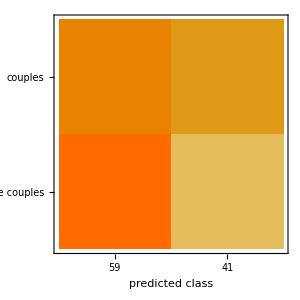

```mathematica
%["ConfusionMatrixPlot"]
```

```mathematica
cl
```

```mathematica
NetInformation[NetModel["ResNet-101 Trained on Augmented CASIA-WebFace Data"],"Layers"]
```

```mathematica
convP = Take[NetModel["ResNet-101 Trained on Augmented CASIA-WebFace Data"], {1, "4b22"}];
```

```mathematica
fmodel2 = NetGraph[{convP, convP, CatenateLayer[], FlattenLayer[], LinearLayer[128], Ramp, LinearLayer[], SoftmaxLayer[]}, {1->3, 2->3, 3->4, 4->5, 5->6, 6->7->8}, "Output"->5];
```

```mathematica
net = NetInitialize[fmodel2]
```

NetGraph[<>]

```mathematica
net
```

NetGraph[<>]

```mathematica
model = NetTrain[net,data , LearningRateMultipliers->{"1"->None, "2"-> None, _->1}]
```

NetTrain::invencin: Invalid input, input is neither a 2D image or a File.

$Failed

```mathematica
NetModel["ResNet-101 Trained on Augmented CASIA-WebFace Data"]
```

NetChain[<>]

Proposal 1
Binary classification

```mathematica
SetDirectory["/Users/Said/Github/Said_Summer2018/Data/KinFaceW-II/images/"]
fatherSon=Import["father-son/fs*"];
dataFatherSon=Flatten@MapThread[{#->"FatherSon"}&,{Partition[fatherSon,2]}];

fatherDaugther=Import["father-dau/fd*"];
dataFatherDaugther=Flatten@MapThread[{#->"FatherDaughter"}&,{Partition[fatherDaughter,2]}];
```

```mathematica
SetDirectory["/Users/Said/Github/Said_Summer2018/Data/KinFaceW-II/images/"]
fatherSon=Import["father-son/fs*"];
dataFatherSon=Flatten@MapThread[{#->"FatherSon"}&,{Partition[fatherSon,2]}];

fatherDaugther=Import["father-dau/fd*"];
dataFatherDaugther=Flatten@MapThread[{#->"FatherDaughter"}&,{Partition[fatherDaughter,2]}];
```

/Users/Said/Github/Said_Summer2018/Data/KinFaceW-II/images/father-son

{{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon,{-Graphics-,-Graphics-}→FatherSon}

```mathematica
Manipulate[ImageAssemble[ImageResize[#,{100,100}]&/@ dataFatherSon⟦i⟧],{i,1,Length[dataFatherSon],1}]
```

```mathematica
averageColor[img_] := Total[Flatten[ImageData[img],1],{1}] / 
(Times @@ ImageDimensions[img])
```

```mathematica
FeatureExtraction[dataFatherSon[[1]][[1]]]
```

FeatureExtraction::mlmpty: The dataset should contain at least one example.

```mathematica
FacialFeatures[dataFatherSon[[1]][[1]],"NosePoints"]
```

{}

```mathematica
dataFatherSon[[1]][[1]]
```

```mathematica
FacialFeatures[dataFatherSon[[5]]]
```

{{},{<|Image→-Graphics-,Age→30,Gender→Female,Emotion→sadness|>}}

```mathematica
features=NetModel["ResNet-101 Trained on Augmented CASIA-WebFace Data"][fatherSon];
```

```mathematica
points=DimensionReduce[features,2,Method-> "TSNE"]
```

```mathematica
Dimensions[points]
```

{500,2}

```mathematica
Graphics[MapThread[Inset[#1,#2,{0,0},0.5]&, {fatherSon,points}], ImageSize->Full, ImagePadding->25]
```

-Graphics-

```mathematica
FeatureNearest[fatherSon, -Graphics-, 5, 
 FeatureExtractor -> 
  NetModel["ResNet-101 Trained on Augmented Casia WebFace Data"]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}